### Constants

```mathematica
SetDirectory[nbdir=NotebookDirectory[]]
```

/Users/thomasbouley/Desktop/MSpect

```mathematica
c=299792458;(*Speed of light in m/s*)
ℏ=6.582119569 10^-16;(*ℏ in eV*s*)
Mpl=1.220 10^19; (*Plank mass is GeV*)
Mhiggs=125.25 ;(*Higgs mass in GeV*)
```

```mathematica
λdm[mDM_]:=ℏ c/mDM (*Compton wavelength in meters given the DM mass in eV*)
φ0mDM=7.2 10^-31(*eV*)
```

7.2×10^-31

```mathematica
(*vDM=1. 10^-3;(*Virial Velocity of the dark matter in units of c*)*)
vDM=220. 10^3/Sqrt[2]/c
```

0.000518904

### Dilatonic Charges

```mathematica
Q[mamu_,A_,Z_]=A/mamu{0.093 -0.036 A^(-1/3)-0.02 (A-2 Z)^2/A^2-1.4 10^-4 Z (Z-1) A^(-4/3),1.7 10^-3 (A-2 Z)/A , 5.5 10^-4 Z/A,(-1.4 +8.2 Z/A +7.7 Z (Z-1) A^(-4/3)) 10^-4};(*{Subscript[Q, m̂],Subscript[Q, δm],Subscript[Q, Subscript[m, e]],Subscript[Q, e]} from eq 73-76 in arXiv:1007.2792 with Subscript[F, A] set to 1*)
Q[A_,Z_]=Q[A,A,Z];
Qp[A_,Z_]=Q[A,Z]-{0.093,0,2.75 10^-4, 2.7 10^-4}(*Q' as defined in Hees*)
```

{0.-0.036/A^(1/3)-(0.02 (A-2 Z)^2)/A^2-(0.00014 (-1+Z) Z)/A^(4/3),(0.0017 (A-2 Z))/A,-0.000275+(0.00055 Z)/A,-0.00027+(-1.4+(8.2 Z)/A+(7.7 (-1+Z) Z)/A^(4/3))/10000}

```mathematica
isoTi={{45.96,46,22},{46.95,47,22},{47.95,48,22},{48.95,49,22},{49.94,50,22}};
abuTi={0.0825,0.0744,.7372,0.0541,0.0518};
isoPt={{191.96,192,78},{193.96,194,78},{194.96,195,78},{195.96,196,78},{197.97,198,78}};
abuPt={0.0078,0.3297,0.3383,0.2524,0.0716};
```

```mathematica
Qmix[isoinfo_,isoabu_]:=Module[{masses,massfrac}, masses=Transpose[isoinfo][[1]];massfrac=masses isoabu/Plus@@(masses isoabu);Plus@@(massfrac (Q[#[[1]],#[[2]],#[[3]]]&/@isoinfo))]
```

```mathematica
QBe=Q[9.012,9,4]
QTi=Qmix[isoTi,abuTi]
QPt=Qmix[isoPt,abuPt]
QAl=Q[26.98,27,13]
QTA6V=.9QTi+.06 QAl+.04 Q[50.94,51,23](*Titanium alloy TA6V used in MICROSCOPE*)
QPtRh= .9 QPt+.1 Q[102.91,103,45](*Platinum Rhodium alloy used in MICROSCOPE*)
```

{0.075256,0.000188637,0.000244119,0.000717058}

{0.0826644,0.000139154,0.000252775,0.00228289}

{0.0852631,0.000340864,0.000219916,0.00427526}

{0.0807628,0.0000630096,0.000265011,0.00173907}

{0.0825566,0.000135694,0.000253332,0.00225065}

{0.0851869,0.000328253,0.000221974,0.00418562}

```mathematica
α2[dv_,Q_]:=dv[[1]]+(dv[[2;;4]]-dv[[1]]).Q[[;;3]]+dv[[5]] Q[[4]]
α2[{dg,d m̂,dδm,dme,de},{Qmh,Qδm,Qme,Qe}]
```

dg+de Qe+(-dg+dme) Qme+(-dg+dδm) Qδm+Qmh (-dg+d m̂)

```mathematica
α1[dv_,Q_]:=α2[dv,Q]
```

```mathematica
dve[d_]=d{0,0,0,0,1};
dvmh[d_]= d{0,1,0,0,0};
dvme[d_]=d{0,0,0,1,0};
dvh[d_]=d{2/9,1,1,1,0};
dvu[d_]=d{1,1,1,1,0};
```

```mathematica
α2[dvu[d],{Qmh,Qδm,Qme,Qe}]
```

d

### Earth Properties

```mathematica
RE=6.3781 10^6;(*Earth radius in meters*) 
GME=3.986004418 10^14;(* Earth's standard gravitational parameter in m^3*s^-2*)
VEs=GME/(RE c^2); (*Unitless gravitational potential on Earth's surface*)
```

The section finds the  dilatonic charge vector for the Earth. The earth in modeled as a uniform sphere composed of a 1:1:1 mixture of Si

```mathematica
Earthcompn={3,1,1,1};(*Approximate  compisition of the earth: number fractions of {^16 O,^24 Mg,^28 Si,^56 Fe} from arXiv:2111.14351*)
isoEarth ={{16.00,16,8},{23.99,24,12},{27.98,28,14},{55.93,56,26}};(*{Mass is amu,A,Z} of {^16 O,^24 Mg,^28 Si,^56 Fe} *)
Qearth=Qmix[isoEarth,Earthcompn];
```

### Earth DM profile

```mathematica
Jp[x_]=3(x-Tanh[x])/x^3;
s2earth[dv_]:=α2[dv,Qearth]Jp[Sqrt[3 α2[dv,Qearth] VEs]]
φampAboveEarth[dv_,mphi_,h_]:= φ0mDM/mphi(1-s2earth[dv]GME/(c^2 (RE+h)))
```

```mathematica
Ip[x_]=3(x Cosh[x]-Sinh[x])/x^3;
sIp[x_]=Normal[Series[Ip[x],{x,0,4}]];
Ipb[x_]=Piecewise[{{sIp[x],Abs[x]<0.04}},Ip[x]];
s1earth[dv_,mdm_]:=α1[dv,Qearth]Ipb[RE/λdm[mdm]]
φfromEarth[dv_,mphi_,h_]:= -s1earth[dv,mphi] GME/(c^2 (RE+h))Exp[-(RE+h)/λdm[mphi]]
```

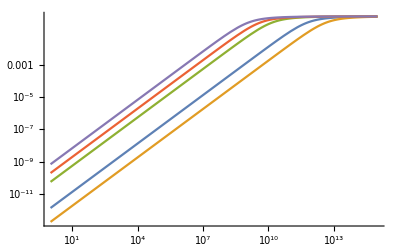

```mathematica
Plot[{s2earth[dve[d]]VEs,s2earth[dvme[d]]VEs,s2earth[dvmh[d]]VEs,s2earth[dvh[d]]VEs,s2earth[dvu[d]]VEs},{d,1,10^15},ScalingFunctions->{"Log10","Log10"}]
```

```mathematica
Manipulate[Plot[{φampAboveEarth[dvu[10^ld],10^-15,10^3 h]/(φ0mDM/10^-15)},{h,0,5 RE/1000},PlotRange->{0,1},FrameLabel->{"Altitude km","DM desity as a fraction of φ_0"},PlotLabel->"du="<>ToString[10^ld,FormatType->StandardForm] ,Frame->True],{ld,0,20}]
```

### Molecular Spectroscopy

This is Q_B in equation 11 in  doi.org/10.1103/PhysRevLett .129 .031302   the letter k is used to be consistent with the conventions in other clock literature e.g. Hees et. al.

```mathematica
kvI2B=2.21{0.027,0.0025,8. 10^-6,0.42,0.9}
```

{0.05967,0.005525,0.00001768,0.9282,1.989}

```mathematica
Plus@@kvI2B[[1;;-2]](*Should be 1 for dimensional analysis reasons*)
%+2.21 0.0013
```

0.993413

0.996286

```mathematica
kMSpec1[dv_,kv_]:=dv.kv
kMSpec2[dv_,kv_]:=dv.kv/2
```

```mathematica
ampMSpec1[dv_,kv_,mdm_]:=RealAbs[kMSpec1[dv,kv]]φ0mDM/mdm
ampMSpec2[dv_,kv_,mdm_,h_]:=RealAbs[kMSpec2[dv,kv]]/2 (φ0mDM/mdm)^2(1-s2earth[dv] GME/(c^2 (RE+h)))^2
```

```mathematica
ampMSpecI2B1[dv_,mdm_]:=ampMSpec1[dv,kvI2B,mdm]
ampMSpecI2B2[dv_,mdm_,h_]:=ampMSpec2[dv,kvI2B,mdm,h]
```

```mathematica
ampMSpec2[dv_,kv_,mdm_]:=ampMSpec2[dv,kv,mdm,0]
ampMSpecI2B2[dv_,mdm_]:=ampMSpec2[dv,kvI2B,mdm,0]
```

```mathematica
MSpecI2Bsig={Log10[#1 2.Pi],Log10[#2] -15.}&@@@Import["DigitizedData/ExpB.csv","CSV"][[3;;]];(*From Figure 2b in doi.org/10.1103/PhysRevLett.129.031302*)
```

```mathematica
MSpecI2Bamp=10^MSpecI2Bsig[[All,2]];
MSpecI2Bmφ1=ℏ 10^MSpecI2Bsig[[All,1]];
MSpecI2Bmφ2=MSpecI2Bmφ1/2;
```

```mathematica
I2Bde1cons=Transpose[{MSpecI2Bmφ1,Table[sol=NSolve[ampMSpecI2B1[dve[d],MSpecI2Bmφ1[[n]]]==MSpecI2Bamp[[n]]&&d>0,d];d/.sol[[1]],{n,1,Length[MSpecI2Bsig]}]}];
```

```mathematica
I2Bdme1cons=Transpose[{MSpecI2Bmφ1,Table[sol=NSolve[ampMSpecI2B1[dvme[d],MSpecI2Bmφ1[[n]]]==MSpecI2Bamp[[n]]&&d>0,d];d/.sol[[1]],{n,1,Length[MSpecI2Bsig]}]}];
```

```mathematica
I2BQNdcons=Transpose[{MSpecI2Bmφ1,Table[sol=NSolve[ampMSpecI2B1[d{0.994,0.096,3. 10^-4,0,0},MSpecI2Bmφ1[[n]]]==MSpecI2Bamp[[n]]&&d>0,d];d/.sol[[1]],{n,1,Length[MSpecI2Bsig]}]}];
```

```mathematica
digitizedI2Bde1=Import["DigitizedData/Deplt.csv","csv"][[3;;]];
digitizedI2Bdme1=Import["DigitizedData/Dmeplt.csv","csv"][[3;;]];
```

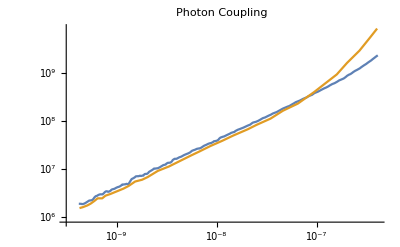

```mathematica
ListLogLogPlot[{I2Bde1cons,digitizedI2Bde1},Joined->True,PlotRange->All,PlotLabel->"Photon Coupling"]
```

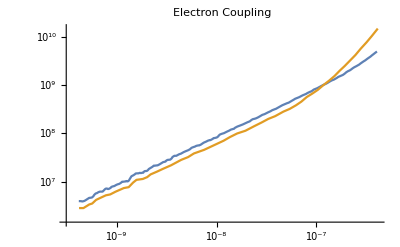

```mathematica
ListLogLogPlot[{I2Bdme1cons,digitizedI2Bdme1},Joined->True,PlotRange->All,PlotLabel->"Electron Coupling"]
```

```mathematica
digitizedI2BQNd=Import["DigitizedData/QNdplt.csv","csv"][[3;;]];
```

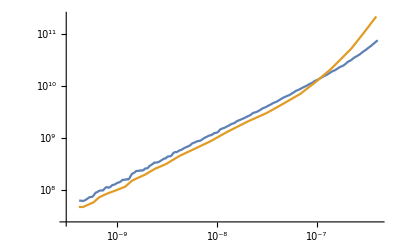

```mathematica
ListLogLogPlot[{I2BQNdcons,digitizedI2BQNd},Joined->True,PlotRange->All]
```

```mathematica
(*dmlineshape[f_,fdm_]:=Sqrt[2/Pi] 1/(vDM vg fdm)Exp[*)
```

```mathematica
lineshape[x_,α_,β_]=α/Sqrt[π β]Exp[-α x-β]Sinh[ Sqrt[4 α β x]]HeavisideTheta[x]
intshape[x_,α_,β_]=Integrate[lineshape[x,α,β],x]
intshape[0,α,β]
```

(ⅇ^(-x α-β) α HeavisideTheta[x] Sinh[2 √(x α β)])/(√π √β)

((-ⅇ^(-x α-β-2 √(x α β)) (-1+ⅇ^(4 √(x α β)))+√π √β Erf[(-β+√(x α β))/(√β)]+√π √β Erf[(β+√(x α β))/(√β)]) HeavisideTheta[x])/(2 √π √β)

0

```mathematica
Manipulate[Plot[lineshape[x,1,β],{x,0,10},PlotRange->{0,0.5}],{β,0.01,3}]
```

```mathematica
Manipulate[Plot[intshape[x,1,β],{x,0,10},PlotRange->{0,1}],{β,0.01,3}]
```

```mathematica
vlab=Quantity[232.,"km/s"]/Quantity["SpeedOfLight"]
βphys=vlab^2/(2 vDM^2)
αphys=1/vDM^2
```

0.000773869

1.11207

3.71386×10^6

```mathematica
c
```

299792458

```mathematica
dmlineshape[f_,fdm_]=1/fdm lineshape[(f-fdm)/fdm,αphys,βphys];
dmintshape[f_,fdm_]= intshape[(f-fdm)/fdm,αphys,βphys];
```

```mathematica
dmlineshapevar[f_,fdm_,vlabt_,vDMt_]=1/fdm lineshape[(f-fdm)/fdm,1/vDMt^2,vlabt^2/(2 vDMt^2)];
```

```mathematica
Manipulate[Plot[dmlineshapevar[f,1,vlabt,vDMt],{f,1,1+10^-5}],{vlabt,Quantity[220.,"km/s"]/Quantity["SpeedOfLight"],Quantity[240.,"km/s"]/Quantity["SpeedOfLight"]},{vDMt,Quantity[220.,"km/s"]/Quantity["SpeedOfLight"],Quantity[240.,"km/s"]/Quantity["SpeedOfLight"]}]
```

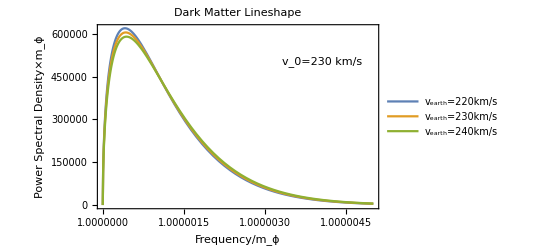

```mathematica
plt1=Plot[{dmlineshapevar[f,1,220 10^3/c,230 10^3/c],dmlineshapevar[f,1,230 10^3/c,230 10^3/c],dmlineshapevar[f,1,240 10^3/c,230 10^3/c]},{f,1,1+5. 10^-6},FrameLabel->{"Frequency/m_ϕ","Power Spectral Density×m_ϕ"},Frame->{{True,False},{True,False}},PlotLabel->"Dark Matter Lineshape",PlotLegends->{"v_earth=220km/s","v_earth=230km/s","v_earth=240km/s"},Epilog->Inset["v_0=230 km/s",Scaled[{.8,.8}]]]
```

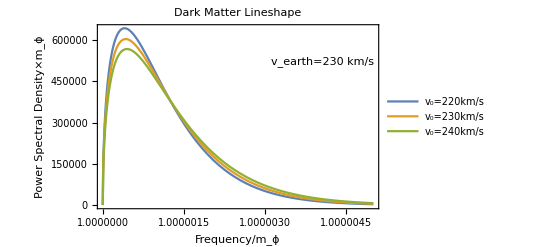

```mathematica
plt2=Plot[{dmlineshapevar[f,1,230 10^3/c,220 10^3/c],dmlineshapevar[f,1,230 10^3/c,230 10^3/c],dmlineshapevar[f,1,230 10^3/c,240 10^3/c]},{f,1,1+5. 10^-6},FrameLabel->{"Frequency/m_ϕ","Power Spectral Density×m_ϕ"},Frame->{{True,False},{True,False}},PlotLabel->"Dark Matter Lineshape",PlotLegends->{"v_0=220km/s","v_0=230km/s","v_0=240km/s"},Epilog->Inset["v_earth=230 km/s",Scaled[{.8,.8}]]]
```

```mathematica
Export["~/Desktop/plt1.pdf",plt1,"pdf"]
Export["~/Desktop/plt2.pdf",plt2,"pdf"]
```

~/Desktop/plt1.pdf

~/Desktop/plt2.pdf

```mathematica
NMaximize[{lineshape[x,1,βphys],x>0},x]
xmaxphys=x/αphys/.%[[2]]
```

{0.264524,{x→1.16038}}

3.12446×10^-7

```mathematica
binwidth=37.7;
stepsize=10.;
```

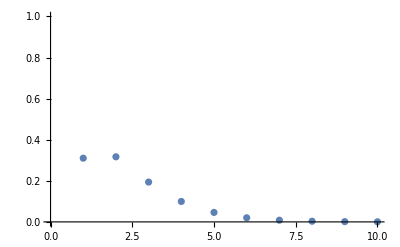

```mathematica
With[{fdm= 10^8},ListPlot[Table[dmintshape[fdm+n binwidth ,fdm]-dmintshape[fdm+(n-1) binwidth ,fdm],{n,1,10}],PlotRange->{0,1}]]
```

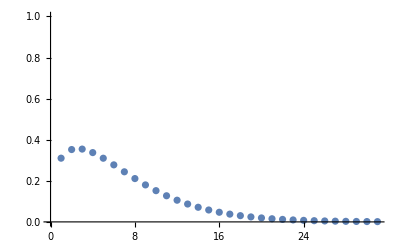

```mathematica
With[{fdm= 10^8},ListPlot[Table[dmintshape[fdm+n stepsize+binwidth ,fdm]-dmintshape[fdm+n stepsize ,fdm],{n,0,30}],PlotRange->{0,1}]]
```

```mathematica
DecoherencePenaltyv1[fdm_]:=If[fdm>2 10^6,Max[Table[dmintshape[fdm+n stepsize+binwidth ,fdm]-dmintshape[fdm+n stepsize ,fdm],{n,0,20}]],1]
DecoherencePenaltyv2[fdm_]:=If[fdm>2 10^6,dmintshape[fdm(xmaxphys+1)+binwidth/2 ,fdm]-dmintshape[fdm(xmaxphys+1)-binwidth/2,fdm],1]
DecoherencePenaltyv3[fdm_]:=If[fdm>2 10^6,Max[Table[dmintshape[fdm+n binwidth ,fdm]-dmintshape[fdm+(n-1) binwidth ,fdm],{n,1,10}]],1]
```

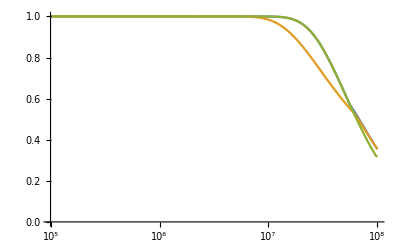

```mathematica
LogLinearPlot[{DecoherencePenaltyv1[ fdm],DecoherencePenaltyv2[fdm],DecoherencePenaltyv3[fdm]},{fdm,10^5,10^8},PlotRange->{0,1}]
```

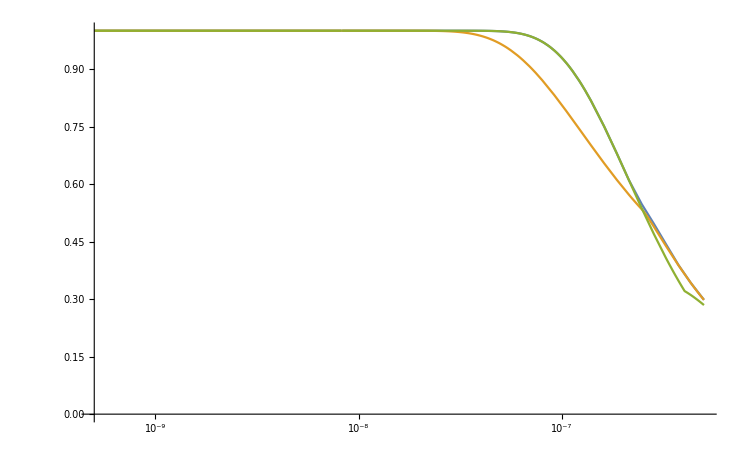

```mathematica
LogLinearPlot[{DecoherencePenaltyv1[ mdm/(2Pi ℏ)],DecoherencePenaltyv2[ mdm/(2Pi ℏ)],DecoherencePenaltyv3[ mdm/(2Pi ℏ)]},{mdm,5. 10^-10,5. 10^-7},PlotRange->{0,1}]
```

```mathematica
DecoherencePenalty=DecoherencePenaltyv1
```

DecoherencePenaltyv1

```mathematica
I2Bde1conswdec={#1,#2 /DecoherencePenalty[#1/(2Pi ℏ)]}&@@@I2Bde1cons;
I2Bdme1conswdec={#1,#2 /DecoherencePenalty[#1/(2Pi ℏ)]}&@@@I2Bdme1cons;
I2BQNdconswdec={#1,#2 /DecoherencePenalty[#1/(2Pi ℏ)]}&@@@I2BQNdcons;
```

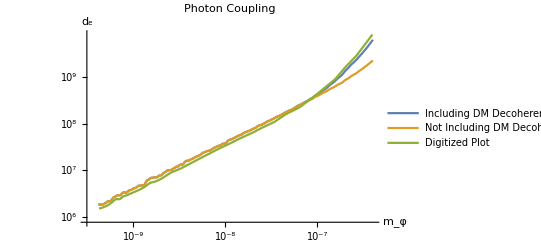

```mathematica
MSpecdeplt=ListLogLogPlot[{I2Bde1conswdec,I2Bde1cons,digitizedI2Bde1},Joined->True,PlotRange->All,PlotLabel->"Photon Coupling",AxesLabel->{"m_φ","d_e"},PlotLegends->{"Including DM Decoherence","Not Including DM Decoherence","Digitized Plot"}]
```

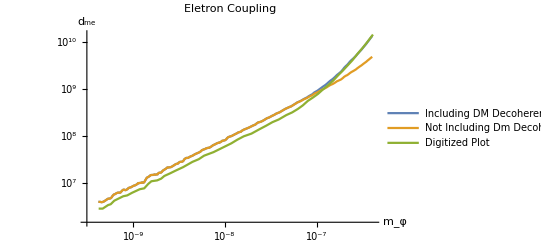

```mathematica
MSpecdmeplt=ListLogLogPlot[{I2Bdme1conswdec,I2Bdme1cons,digitizedI2Bdme1},Joined->True,PlotRange->All,PlotLabel->"Eletron Coupling",AxesLabel->{"m_φ","d_me"},PlotLegends->{"Including DM Decoherence","Not Including Dm Decoherence","Digitized Plot"}]
```

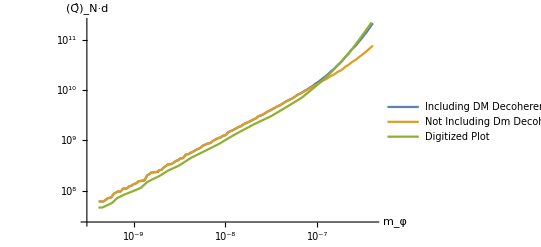

```mathematica
MSpecQNdplt=ListLogLogPlot[{I2BQNdconswdec,I2BQNdcons,digitizedI2BQNd},Joined->True,PlotRange->All,AxesLabel->{"m_φ","(Q̂)_N·d"},PlotLegends->{"Including DM Decoherence","Not Including Dm Decoherence","Digitized Plot"}]
```

```mathematica
Export["plts/de.pdf",MSpecdeplt,"pdf"]
Export["plts/dme.pdf",MSpecdmeplt,"pdf"]
Export["plts/QNd.pdf",MSpecQNdplt,"pdf"]
```

plts/de.pdf

plts/dme.pdf

plts/QNd.pdf

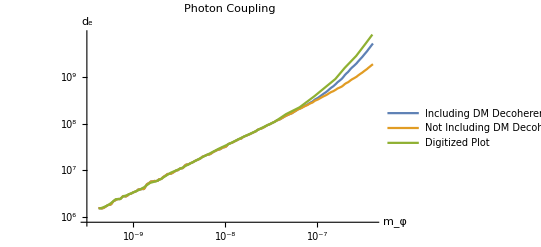

```mathematica
ListLogLogPlot[{{#1,#2/1.2}&@@@I2Bde1conswdec,{#1,#2/1.2}&@@@I2Bde1cons,digitizedI2Bde1},Joined->True,PlotRange->All,PlotLabel->"Photon Coupling",AxesLabel->{"m_φ","d_e"},PlotLegends->{"Including DM Decoherence","Not Including DM Decoherence","Digitized Plot"}]
```

```mathematica
fde1=Interpolation[I2Bde1cons];
gde1=Interpolation[digitizedI2Bde1];
hde1=Interpolation[I2Bde1conswdec];
```

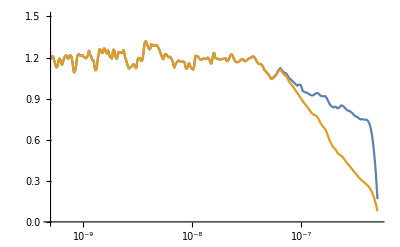

```mathematica
LogLinearPlot[{hde1[mdm]/gde1[mdm],fde1[mdm]/gde1[mdm]},{mdm,5. 10^-10,5. 10^-7},PlotRange->{0,1.5}]
```

```mathematica
fdme1=Interpolation[I2Bdme1cons];
gdme1=Interpolation[digitizedI2Bdme1];
hdme1=Interpolation[I2Bdme1conswdec];
```

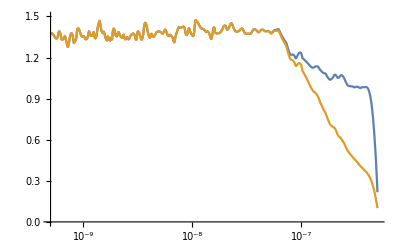

```mathematica
LogLinearPlot[{hdme1[mdm]/gdme1[mdm],fdme1[mdm]/gdme1[mdm]},{mdm,5. 10^-10,5. 10^-7},PlotRange->{0,1.5}]
```

```mathematica
fQNd=Interpolation[I2BQNdcons];
gQNd=Interpolation[digitizedI2BQNd];
hQNd=Interpolation[I2BQNdconswdec];
```

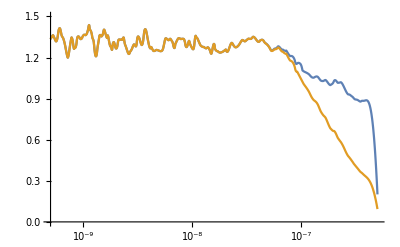

```mathematica
LogLinearPlot[{hQNd[mdm]/gQNd[mdm],fQNd[mdm]/gQNd[mdm]},{mdm,5. 10^-10,5. 10^-7},PlotRange->{0,1.5}]
```